## PERISCOPE Dataset

(https://www.nature.com/articles/s41592-024-02537-7)

### Result #1: Diseases do not cleanly fit into discrete categories

#### TODO

How reliable is UMAP? How robust is this result in our model?

Quantify this distribution

### Non-result (so far): Cell metric distributions vs. CA metric distribution:

#### Distribution of real cell area after single-gene perturbation

```mathematica
dt = OpenRead["Downloads/20200805_A549_WG_Screen_guide_normalized_median_merged_ALLBATCHES_ALLWELLS.csv"];
lines  = {};
headers = ReadLine[dt];
```

```mathematica
Table[AppendTo[lines, ReadLine[dt]], {i, 1000}];
Close[dt]
```

```mathematica
int = ImportString[StringRiffle[lines, "\n"], "CSV"];
```

```mathematica
h2 = StringSplit[headers, ","]
```

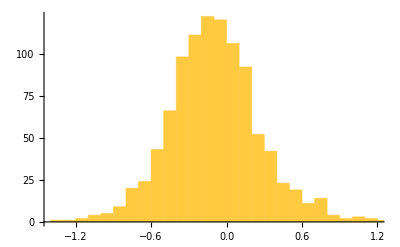

```mathematica
Histogram[int[[All, 3]]]
```

#### Distribution of CA area after single-cell perturbation

```mathematica
polys=Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={400,{-100, 100}}},SeedRandom[6353];
ParallelMap[{{"[◼]", "CAPolygon"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,init,txspec,#,"ReturnPerturbations"->False]]&, {{"[◼]", "allperts"}}[ru,init,txspec]]];
```

```mathematica
areas = Area/@ polys;
```

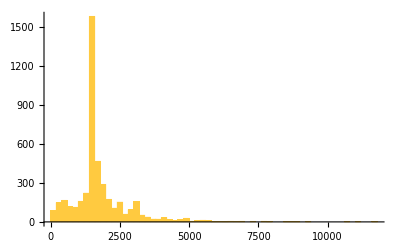

```mathematica
Histogram[areas, PlotRange->All]
```

#### (Other example metrics from dataset)

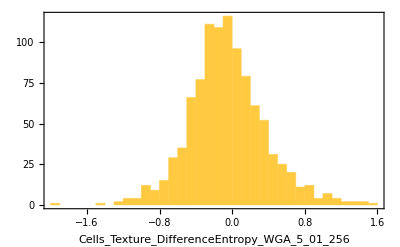
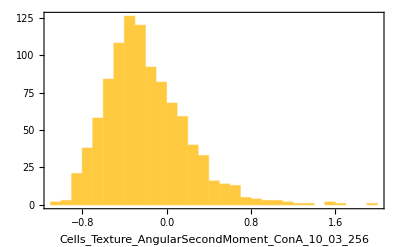
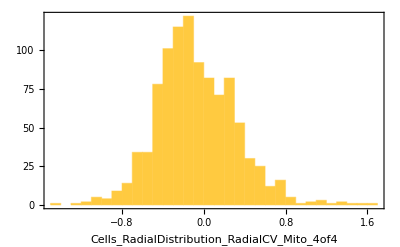
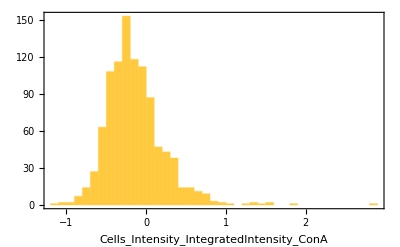
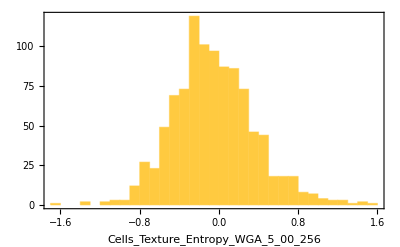
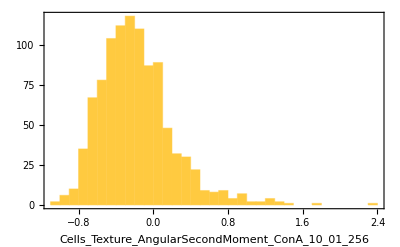
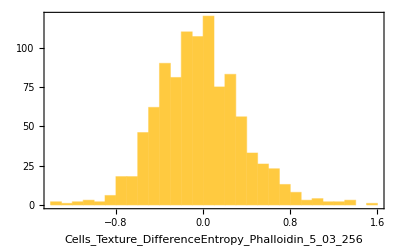
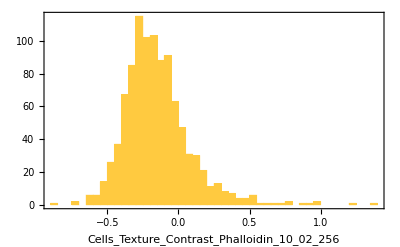
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Histogram[int[[All, #]], Frame->True, FrameLabel->{h2[[#]], Automatic}, PlotRange->All]&/@ RandomSample[Range[1000], 10]
```

#### (Other metrics from us)

```mathematica
Module[{ru={299459058088077823758143088095350287424,4,1}, ca},
ca=CellularAutomaton[ru,{{1},0},{400,{-200,200}}];
lefts = 
ParallelMap[
(-(201-Min[If[Length[#]==1,Infinity,Length[First[#]]]&[Split[#]]&/@#])&)[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{400,{-200,200}},#,"ReturnPerturbations"->False]
]&,{{"[◼]", "allperts"}}[ca,4]
]];
```

```mathematica
Show[
Histogram[
lefts,
{1},{"Log","Probability"},Frame->True,AspectRatio->.4,FrameLabel->{"leftmost offset","frequency"},PlotRange->3, Prolog->{Red, Dotted, Line[{{-5, 0}, {-5, 1}}]}(*, ChartStyle->Lighter[RGBColor[0.96, 0.73, 0], .6]*)],
Graphics[{Thickness[.003],(*Red,*) GrayLevel[0.2],AbsoluteDashing[2,1], Line[{{-5, -9.25}, {-5, 1}}]},Background->Opacity[0, White]]
]
```

#### TODO

Their perturbations are significantly smaller (one gene out of 20,000) need find a way to model smaller perturbations

## IHME Data

### Non-result (so far): Prevalence of disease

```mathematica
hi2 = Import["/Users/erichegonzales/Downloads/IHME-GBD_2021_DATA-772caba6-1/IHME-GBD_2021_DATA-772caba6-1.csv", "Tabular"];
```

```mathematica
ListStepPlot[Callout[#["val"] / Total[hi2[[All, "val"]]], #["cause"]]&/@Normal[ReverseSortBy[hi2, #val&][[All, {"cause", "val"}]]] , ScalingFunctions->{"Log", "Log"}, PlotRange->All]
```

-Graphics-

```mathematica
polys=Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={200,{-10,30}}},SeedRandom[6353];
ReverseSort@*Counts@*({{"[◼]", "CAPolygon"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,init,txspec,#,"ReturnPerturbations"->False]]&/@#&)@{{"[◼]", "allperts"}}[ru,init,txspec]];
```

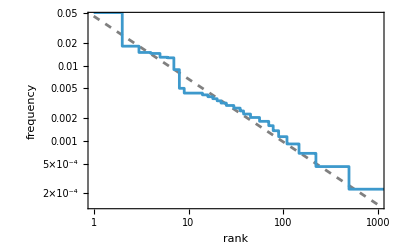

```mathematica
Show[Plot[0.04583459736390076/x^0.8374727002923698,{x,1,1000},ScalingFunctions->{"Log","Log"},PlotStyle->Directive[Dashed,Gray],Frame->True,FrameLabel->{"rank","frequency"}],ListStepPlot[Values[ReverseSort[polys]]/Total[Values[polys]],PlotRange->All,ScalingFunctions->{"Log","Log"},Frame->True,FrameLabel->{"rank","frequency"}]]
```

## Other

### Disease-treatment matrix

#### “Nephew” rule

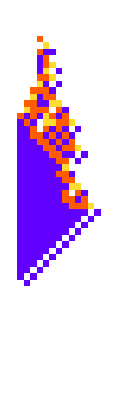

```mathematica
{{"[◼]", "PlotCA"}}[{310092882054357150741373544577593044032,4,1}, "Steps"->50]
```

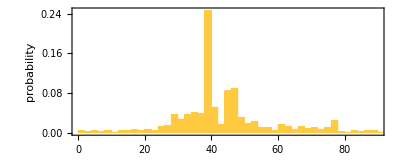

```mathematica
Module[
{ru = {310092882054357150741373544577593044032,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}},Histogram[lts = {{"[◼]", "TestCALifeTime"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru, init, txspec, #, "ReturnPerturbations"->False]]&/@ {{"[◼]", "allperts"}}[ru, init, txspec],  100, "Probability",Frame->True,AspectRatio->.4,FrameLabel->{"lifetime","probability"}]]
```

#### Running

```mathematica
Module[
{ru = {310092882054357150741373544577593044032,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}, aps},
aps = {{"[◼]", "allperts"}}[CellularAutomaton[ru, init, txspec], 4];
dis = Discard[aps, 35<={{"[◼]", "TestCALifeTime"}}[ResourceFunction["PerturbedCellularAutomaton"][ru, init, txspec, #]]<=50&];
Function[pert, {pert, #}&/@ Select[dis, Keys[#][[1, 1]]> Keys[pert][[1, 1]]&]]/@ dis
]
```

```mathematica
ps = Function[pert, {pert, #}&/@ Select[dis, Keys[#][[1, 1]]> Keys[pert][[1, 1]]&]]/@ dis;
```

```mathematica
pfs = Flatten[ps, 1];
```

```mathematica
Module[
{ru = {310092882054357150741373544577593044032,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}, aps},plts = ParallelMap[{{"[◼]", "TestCALifeTime"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru, init, txspec, Join@@#, "ReturnPerturbations"->False]]&, pfs]];
```

```mathematica
plts = ;
```

Clustering of disease to treatment

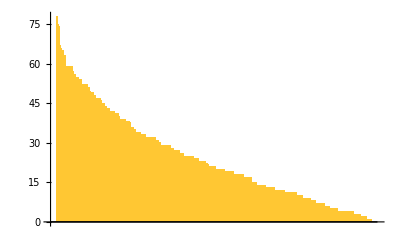

```mathematica
BarChart[Length/@ReverseSortBy[GatherBy[pfs[[Select[Range[Length[pfs]], 35<=plts[[#]]<=50&]]], #[[2]]&], Length]]
```

#### Binary Matrix

```mathematica
ArrayPlot[SparseArray[Join[First[Position[dis, #1]],First[Position[dis, #2]]] ->1&@@@pfs[[Select[Range[Length[pfs]], 37.5<=plts[[#]]<=42.5&]]]]]
```

-Graphics-

```mathematica
ArrayPlot[SparseArray[Join[First[Position[dis, #1]],First[Position[dis, #2]]] ->1&@@@pfs[[Select[Range[Length[pfs]], 20<=plts[[#]]<=60&]]]]]
```

-Graphics-

#### Gradient Matrix

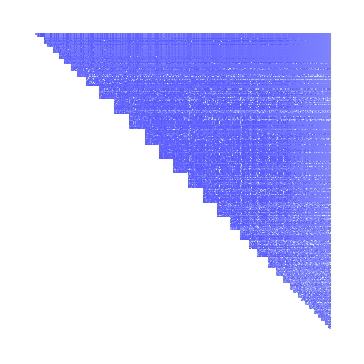

```mathematica
ArrayPlot[arr, ColorRules->{-1->White},ColorFunction->(If[# == -1, White,Blend[{Lighter[Blue],  LightBlue, White},#]]&)]
```

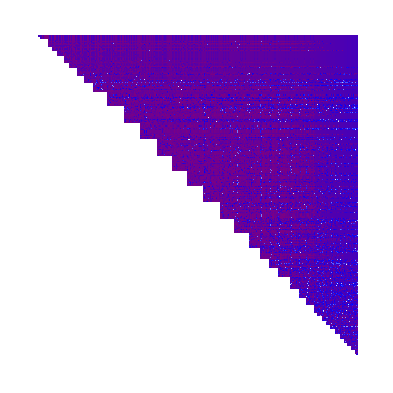

```mathematica
ArrayPlot[arr, ColorRules->{-1->White},ColorFunction->(If[# == -1, White,Blend[{Purple, Blue, LightBlue, White},#]]&)]
```